```mathematica
rawData=(****INPUT NEEDED****)(*need file name/location*)Import["/Users/4tc/Dropbox/suli 2018 project/y_optics_0001/input-dist.mu.txt","Table"];
(*Import["/Users/4tc/Dropbox/suli 2018 project/FromJeff/ExtractedBeam/Beam_Correlated.txt","Table"];
rawData=rawData[[;;5000]];*)
correlationData=Drop[Transpose[rawData],-2];

correlationData=RotateRight[correlationData,2];

numLines=Length@correlationData[[1]];
averages={Mean[correlationData[[1]]],Mean[correlationData[[2]]],Mean[correlationData[[3]]],Mean[correlationData[[4]]]};
(*order: x, xp, y, yp*)
sigMeasMat={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
mod1=Module[{i,j,k},
For[j=1,j≤4,j++,
For[k=1,k≤4,k++,
sigMeasMat[[k,j]]=(1/numLines)*∑_(i=1)^numLines ((correlationData[[k,i]]-averages[[k]])(correlationData[[j,i]]-averages[[j]]));
];
];]
averages;
sigMeasMat=sigMeasMat;  (*convert to mm from m*)
sigMeasMat//MatrixForm  (*COVARIANCE*)

sigX=(sigMeasMat[[1,1]])^(1/2); sigXP=(sigMeasMat[[2,2]])^(1/2); sigY=(sigMeasMat[[3,3]])^(1/2); sigYP=(sigMeasMat[[4,4]])^(1/2);
sigList={sigX,sigXP,sigY,sigYP} 
sigMeasMat2=Table[
sigMeasMat[[m,n]]/(sigList[[m]]*sigList[[n]])
,{m,1,4}
,{n,1,4}
];
MatrixForm@sigMeasMat2 (*PEARSON CORRELATIONS*)
```

(0.000134291 | -3.94625×10^-7 | -3.94625×10^-7 | -1.61416×10^-7
-3.94625×10^-7 | 0.000237861 | 0.000237861 | 0.0000806622
-3.94625×10^-7 | 0.000237861 | 0.000237861 | 0.0000806622
-1.61416×10^-7 | 0.0000806622 | 0.0000806622 | 0.00002777)

{0.0115884,0.0154228,0.0154228,0.00526972}

(1. | -0.002208 | -0.002208 | -0.00264323
-0.002208 | 1. | 1. | 0.992476
-0.002208 | 1. | 1. | 0.992476
-0.00264323 | 0.992476 | 0.992476 | 1.)

```mathematica
(* x results from helper*)
({{243.56394880078702, 82.56092345751053, 0.05192968215899896, -0.02345060192267745}, {0, 28.420747508445867, 0.01174098916652989, -0.005577549094394231}, {0, 0, 139.05231065226417, -44.73240482203925}, {0, 0, 0, 15.152317355929005}})
(* x results from here*)
({{236.66754850442462, 80.23737920120772, 0.6818088476087235, 236.66754850442462}, {80.23737920120772, 27.626437206146164, 0.24313251157359603, 80.23737920120772}, {0.6818088476087235, 0.24313251157359603, 135.13608943925274, 0.6818088476087235}, {236.66754850442462, 80.23737920120772, 0.6818088476087235, 236.66754850442462}})
```

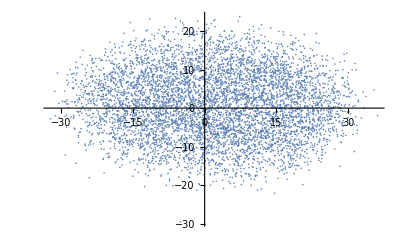

```mathematica
ListPlot[
rawData[[;;;;100,{1,3}]]
]
```

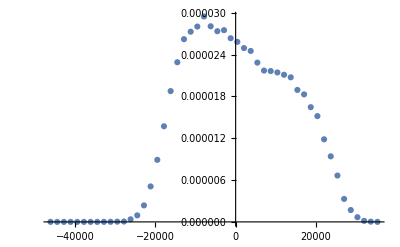

```mathematica
ListPlot[
Import[dataWSD[[1]],"Table"][[;;,{2,3}]]
]
```

```mathematica
({{-2.346383976244612*^6, 294208.80116984516, -76032.62121554243, 157431.72792740038}, {0, 571884.058013023, -126035.35364890198, 84204.43246225505}, {0, 0, 134.50297972837663, -48.66618882587794}, {0, 0, 0, 20.469154294584754}})
```

```mathematica
({{189.4551396794065, 58.731590123804985, -3.2317444876277994, 1.6979097050069223}, {58.731590123804985, 18.297144439943057, -1.0544717713394978, 0.5530611557384746}, {-3.2317444876277994, -1.0544717713394978, 71.76122767695838, -22.55275110210136}, {1.6979097050069223, 0.5530611557384746, -22.55275110210136, 7.431391936163925}})
```

```mathematica
correlationData[[4]]
```

{0.0138199,0.000355332,-0.000510848,-0.0217212,0.00464172,-0.00318187,-0.0145298,0.00578475,0.0247681,-0.0159537,4980,-0.00819256,0.000302171,-0.00530652,0.0183775,0.00467184,-0.0179775,0.0000648986,0.0194276,0.00626435,-0.00171197}
 |  |  |  |